# In Class Demo - 3 May 2024

## Return at 8:36am!

```mathematica
f[x_,y_] = x y - x +y;
g[x_,y_] = x - x^2- y;
h[x_] = Sum[Subscript[a, j] x^j,{j,0,5}]
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5

```mathematica
eqn = g[x,h[x]]- D[h[x],x]f[x,h[x]]
Expand[eqn]
```

x-x^2-a_0-x a_1-x^2 a_2-x^3 a_3-x^4 a_4-x^5 a_5-(a_1+2 x a_2+3 x^2 a_3+4 x^3 a_4+5 x^4 a_5) (-x+a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5+x (a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4+x^5 a_5))

x-x^2-a_0-a_0 a_1-x a_0 a_1-x a_1^2-x^2 a_1^2+x^2 a_2-2 x a_0 a_2-2 x^2 a_0 a_2-3 x^2 a_1 a_2-3 x^3 a_1 a_2-2 x^3 a_2^2-2 x^4 a_2^2+2 x^3 a_3-3 x^2 a_0 a_3-3 x^3 a_0 a_3-4 x^3 a_1 a_3-4 x^4 a_1 a_3-5 x^4 a_2 a_3-5 x^5 a_2 a_3-3 x^5 a_3^2-3 x^6 a_3^2+3 x^4 a_4-4 x^3 a_0 a_4-4 x^4 a_0 a_4-5 x^4 a_1 a_4-5 x^5 a_1 a_4-6 x^5 a_2 a_4-6 x^6 a_2 a_4-7 x^6 a_3 a_4-7 x^7 a_3 a_4-4 x^7 a_4^2-4 x^8 a_4^2+4 x^5 a_5-5 x^4 a_0 a_5-5 x^5 a_0 a_5-6 x^5 a_1 a_5-6 x^6 a_1 a_5-7 x^6 a_2 a_5-7 x^7 a_2 a_5-8 x^7 a_3 a_5-8 x^8 a_3 a_5-9 x^8 a_4 a_5-9 x^9 a_4 a_5-5 x^9 a_5^2-5 x^10 a_5^2

```mathematica
coeffs=CoefficientList[Expand[eqn],x]
```

{-a_0-a_0 a_1,1-a_0 a_1-a_1^2-2 a_0 a_2,-1-a_1^2+a_2-2 a_0 a_2-3 a_1 a_2-3 a_0 a_3,-3 a_1 a_2-2 a_2^2+2 a_3-3 a_0 a_3-4 a_1 a_3-4 a_0 a_4,-2 a_2^2-4 a_1 a_3-5 a_2 a_3+3 a_4-4 a_0 a_4-5 a_1 a_4-5 a_0 a_5,-5 a_2 a_3-3 a_3^2-5 a_1 a_4-6 a_2 a_4+4 a_5-5 a_0 a_5-6 a_1 a_5,-3 a_3^2-6 a_2 a_4-7 a_3 a_4-6 a_1 a_5-7 a_2 a_5,-7 a_3 a_4-4 a_4^2-7 a_2 a_5-8 a_3 a_5,-4 a_4^2-8 a_3 a_5-9 a_4 a_5,-9 a_4 a_5-5 a_5^2,-5 a_5^2}

```mathematica
coeffs[[5]]/.rules
```

0

```mathematica
rules={Subscript[a, 0]->0,Subscript[a, 1]->1,Subscript[a, 2]->-1,Subscript[a, 3]->1/2,Subscript[a, 4]->-3/4,Subscript[a, 5]->0}
```

{a_0→0,a_1→1,a_2→-1,a_3→1/2,a_4→-3/4,a_5→0}

```mathematica
h[x]/.rules
```

x-x^2+x^3/2-(3 x^4)/4

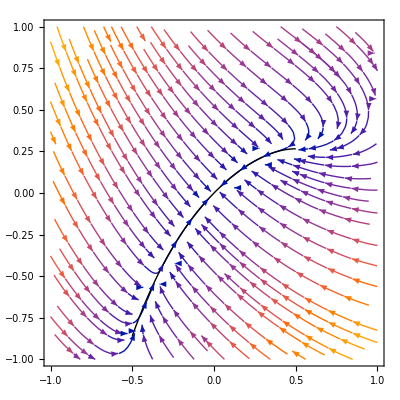

```mathematica
p1=StreamPlot[{f[x,y],g[x,y]},{x,-1,1},{y,-1,1}];
p2=Plot[{h[x]/.rules},{x,-1/2,1/2},PlotStyle->{{Black,Thick}}];
Show[p1,p2]
```